Интегралы вида ∫_(-∞)^∞ f(x)ⅆx, где f(x) - функция непрерывная на  (-∞;∞), аналитическая в верхней полуплоскости, за исключением конечного числа особых точек z1....zn, лежащих в конечной части верхней полуплоскости вычисляется:

∫_(-∞)^∞ f(x)ⅆx=2π ⅈ∑_(i=1)^n res(f(z),z→ z_k)

Рассмотрим пример:

##### №12.461

Вычислить интеграл, используя описанный выше способ:

∫_(-∞)^∞ (x^4+1)/(x^6+1)ⅆx

Зададим функцию

```mathematica
f[x_]:=(x^4+1)/(x^6+1)
```

Посчитаем интеграл “в лоб”, замеряя время.

```mathematica
Integrate[f[x],{x,-Infinity,Infinity}]//Timing
```

{0.187201,(4 π)/3}

Получили не такой уж и плохой по времени результат, но все же некоторое время уходит на его высчет.

Воспользуемся способом (1).

Для этого найдем все полюса:

```mathematica
sol=Solve[z^6+1==0,z]
```

{{z→-ⅈ},{z→ⅈ},{z→-(-1)^(1/6)},{z→(-1)^(1/6)},{z→-(-1)^(5/6)},{z→(-1)^(5/6)}}

Теперь выберем из них только те, что лежат в верхней полуплоскости ( Im[z_i]>0):

```mathematica
sol1=Table[If[Im[z/.sol[[i]]]>0,sol[[i]],Nothing],{i,1,Length[sol]}]
```

{{z→ⅈ},{z→(-1)^(1/6)},{z→(-1)^(5/6)}}

Изобразим их на комплексной плоскости:

```mathematica
Graphics[{PointSize[Large],Red,Point[ReIm[z/.sol1]]},Axes->True,PlotRange->{{-1,1},{0,2}},AxesLabel->{Re,Im}]
```

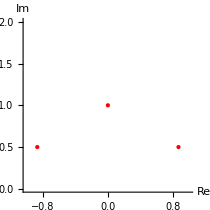

Теперь найдем значение интеграла согласно (1):

```mathematica
int=2 ⅈ π Sum[Residue[f[z],{z,z/.sol1[[i]]}],{i,1,Length[sol1]}]//ComplexExpand//Timing
```

{0.,(4 π)/3}

Получили тотже самый ответ, но за гораздо меньший промежуток времени.

Итак в итоге имеем:

∫_(-∞)^∞ f(x)ⅆx=(4 π)/3

Способы, описанные выше, можно применить ко всем задачам №№12.450-470, что рекомендуется проделать самостоятельно.